## Problem 2b

```mathematica
2*Zeta[3]/Pi^2*(1.38*10^-23)^3*300^3/((1.054*10^-34)^3*(3*10^8)^3)
```

5.46727×10^14

## Problem 4 c

x = lambda/(hc)

```mathematica
dUdy[kbT_]:=(kbT*x)^-5/(Exp[1/(kbT*x)]-1);
```

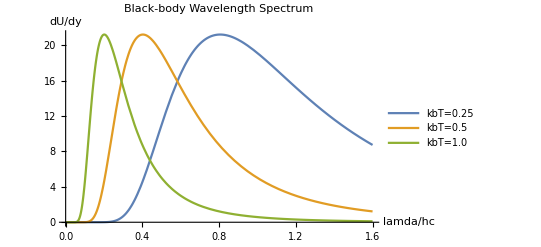

```mathematica
Plot[{dUdy[0.25],dUdy[0.5],dUdy[1.0]},{x,0,1.6},AxesLabel->{lamda/hc,dU/dy},PlotLabel->"Black-body Wavelength Spectrum",PlotLegends->{"kbT=0.25","kbT=0.5","kbT=1.0"}]
```

## Problem 4 d

```mathematica
(* Define unitless variable y *)
```

General::munfl: 2.68046×10^22 1.0434538353×10^-13287 is too small to represent as a normalized machine number; precision may be lost.

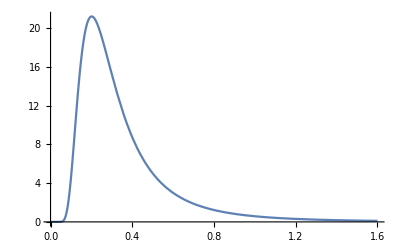

```mathematica
Plot[(y)^-5/(Exp[1/y]-1),{y,0,1.6}]
```

```mathematica
yderivative=D[(y)^-5/(Exp[1/y]-1),y];
```

```mathematica
FindRoot[yderivative,{y,0.15}]
```

{y→0.201405}

```mathematica
ypeak=0.20141;
```

```mathematica
c=299792458;
kb=1.380649*10^-23;
h=6.62607015*10^-34;
lambdapeak=ypeak*(h*c/(kb*T));
```

```mathematica
(* Answer *)
```

```mathematica
lambdapeak*T
```

0.00289784

Yes, lambdapeak T = 0.2898 mK

## Problem 4 e

```mathematica
lambdapeak
```

0.00289784/T

```mathematica
(* Now, replace 6000 K for T *)
```

```mathematica
lambdapeaksun=0.002898/6000
```

4.83×10^-7

```mathematica
lambdapeakexam=0.002898/1.2*10^3
```

2.415

```mathematica
(* We want it in nanometers *)
```

```mathematica
lambdapeaksun*10^9
```

483.

The answer for the peak wavelength is 483 nm